# Analysis of representative paintings and determination of period they belong to

more about artistic periods by doing analysis of the intensities of the pixels of paintings of some famous artisits from four particular art movements: Renaissance, Baroque, Impressionism and Cubism, so to learn more about each period. Afterwards I will classify the paintings in categories, and compare how efficient is the classification with Classify[].

Liubove Orlov Savko, Jun. 30,  2018

Some of my favourite things to do is read about artworks and visit museums. I recently went to the Museum of Fine Arts where I saw some amazing collection of  paintings. Each period has certain characteristics which I would like to analyze using the powerful tools the Wolfram Mathematica Language offers. All period has an enormous amount of artists, and Wolfram Data Repository has a lot of data available. I will take only the most representative artists of each period, and try to have equally-sized data sets of each period and afterwards do comparison of some ImageMeasurements[], specifically the intensities of pixels in the paintings. For the comparision the boxplot functions will visualize in an intepretable manner, revealing some features of each art movement.  I will do analysis of four art movements in particular: impressionism, baroque, renaissance and cubism. Besides doing intensity analysis I will next use classify function and see how accurate it actually may classify the art. I will do this to classify the paintings in four periods. Next I will do the same for classificaction of painting to their artists them selves. For achieving this I will use the Classify[] function.

## Renaissance

Spans fourteenth and seventeenth centuries. Many argue that the ideas characterizing the Renaissance had their origin in late 13th-century Florence, in particular with the writings of Dante Alighieri  and Petrarch, as well as the paintings of Giotto di Bondone. Some writers date the Renaissance quite precisely; one proposed starting point is 1401, when the rival geniuses Lorenzo Ghiberti and Filippo Brunelleschi competed for the contract to build the bronze doors for the Baptistery of the Florence Cathedral (Ghiberti won). Others see more general competition between artists and polymaths such as Brunelleschi, Ghiberti, Donatello, and Masaccio for artistic commissions as sparking the creativity of the Renaissance. Yet it remains much debated why the Renaissance began in Italy, and why it began when it did. Accordingly, several theories have been put forward to explain its origins. It has long been a matter of debate why the Renaissance began in Florence, and not elsewhere in Italy. Scholars have noted several features unique to Florentine cultural life that may have caused such a cultural movement. Many have emphasized the role played by the Medici, a banking family and later ducal ruling house, in patronizing and stimulating the arts. Lorenzo de Medici was the catalyst for an enormous amount of arts patronage, encouraging his countrymen to commission works from the leading artists of Florence, including Leonardo da Vinci, Sandro Botticelli, and Michelangelo Buonarroti.1 The artists that were used for data were El Greco, Leonardo da Vinci, Titian, Michelangelo and Sandro Botticelli.

Extract notable artwork of painters of the Renaissance: El Greco, Leonardo da Vinci, Titian, Michelangelo and Sandro Boticelli:

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
greco={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
davinci={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
titian={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
michelangelo={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
botticcelli={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

Save all sets of paintings in one variable:

```mathematica
renaissance=Join[davinci,titian,michelangelo,botticcelli,greco];
```

## Baroque

The Baroque is a highly ornate and often extravagant style of architecture, art and music that flourished in Europe from the early 17th until the late 18th century. It followed the Renaissance style and preceded the Neoclassical style. It was encouraged by the Catholic Church as a means to counter the simplicity and austerity of Protestant architecture, art and music, though Lutheran Baroque art developed in parts of Europe as well. The baroque style used contrast, movement, exuberant detail, grandeur and surprise to achieve a sense of awe. The style began in the first third of the 17th century in Rome, then spread rapidly to France, northern Italy, Spain and Portugal, then to Austria and southern Germany. By the 1730s, it had evolved into an even more flamboyant variant, called rocaille or Rococo, which appeared in France and central Europe until the late 18th century2. The artists I used for data were Rembrandt, Rubens, Diego Velazquez and Caravaggio.

Extract paintings of Rembrandt, Rubens, Diego Velazquez and Caravaggio:

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
rembrandt={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
rubens={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
velazquez={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
caravaggio={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

Save all paintings in one variable:

```mathematica
barroque=Join[rembrandt,rubens,velazquez,caravaggio];
```

## Impressionism

The impressionsm is my favorite art movement. It began in 19th-century characterised by relatively small, thin, yet visible brush strokes, open composition, emphasis on accurate depiction of light in its changing qualities (often accentuating the effects of the passage of time), ordinary subject matter, inclusion of movement as a crucial element of human perception and experience, and unusual visual angles. Impressionism originated with a group of Paris-based artists whose independent exhibitions brought them to prominence during the 1870s and 1880s.

The Impressionists faced harsh opposition from the conventional art community in France. The name of the style derives from the title of a Claude Monet work, Impression, soleil levant (Impression, Sunrise), which provoked the critic Louis Leroy to coin the term in a satirical review published in the Parisian newspaper Le Charivari.

The development of Impressionism in the visual arts was soon followed by analogous styles in other media that became known as impressionist music and impressionist literature. Radicals in their time, early Impressionists violated the rules of academic painting. They constructed their pictures from freely brushed colours that took precedence over lines and contours, following the example of painters such as Eugène Delacroix and J. M. W. Turner. They also painted realistic scenes of modern life, and often painted outdoors. Previously, still lifes and portraits as well as landscapes were usually painted in a studio.[1] The Impressionists found that they could capture the momentary and transient effects of sunlight by painting outdoors or en plein air. They portrayed overall visual effects instead of details, and used short “broken” brush strokes of mixed and pure unmixed colour—not blended smoothly or shaded, as was customary—to achieve an effect of intense colour vibration.

Impressionism emerged in France at the same time that a number of other painters, including the Italian artists known as the Macchiaioli, and Winslow Homer in the United States, were also exploring plein-air painting. The Impressionists, however, developed new techniques specific to the style. Encompassing what its adherents argued was a different way of seeing, it is an art of immediacy and movement, of candid poses and compositions, of the play of light expressed in a bright and varied use of colour.

The public, at first hostile, gradually came to believe that the Impressionists had captured a fresh and original vision, even if the art critics and art establishment disapproved of the new style.

By recreating the sensation in the eye that views the subject, rather than delineating the details of the subject, and by creating a welter of techniques and forms, Impressionism is a precursor of various painting styles, including Neo-Impressionism, Post-Impressionism, Fauvism, and Cubism. 3
Since the data set in the repository of Vincent van Gogh consists of 195 artworks, it is sufficient enough to train network.

Extract Vincen van Gogh’s paintings:

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
vangogh={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

Save this set to the variable of impressionism to follow the convention:

```mathematica
impr=vangogh;
```

## Cubism

Cubism is an early - 20 th - century art movement which brought European painting and sculpture historically forward toward 20 th century Modern art.Cubism in its various forms inspired related movements in literature and architecture.Cubism has been considered to be among the most influential art movements of the 20 th century.[1][2] The term is broadly used in association with a wide variety of art produced in Paris (Montmartre, Montparnasse and Puteaux) during the 1910 s and throughout the 1920 s.The movement was pioneered by Pablo Picasso and Georges Braque, joined by Jean Metzinger, Albert Gleizes, Robert Delaunay, Henri Le Fauconnier, and Fernand Léger.[3] One primary influence that led to Cubism was the representation of three - dimensional form in the late works of Paul Cézanne.[4] A retrospective of Cézanne' s paintings had been held at the Salon d' Automne of 1904, current works were displayed at the 1905 and 1906 Salon d' Automne, followed by two commemorative retrospectives after his death in 1907.[5] In Cubist artwork, objects are analyzed, broken up and reassembled in an abstracted form—instead of depicting objects from a single viewpoint, the artist depicts the subject from a multitude of viewpoints to represent the subject in a greater context.[

The impact of Cubism was far - reaching and wide - ranging.In other countries Futurism, Suprematism, Dada, Constructivism, De Stijl and Art Deco developed in response to Cubism.Early Futurist paintings hold in common with Cubism the fusing of the past and the present, the representation of different views of the subject pictured at the same time, also called multiple perspective, simultaneity or multiplicity, [7] while Constructivism was influenced by Picasso' s technique of constructing sculpture from separate elements.[8] Other common threads between these disparate movements include the faceting or simplification of geometric forms, and the association of mechanization and modern life.4

The main representative of this period is Picasso. Other artists analyzed to do this project were Juan Gris, Georges Braque, Robert Delaunay.

Extract paintings from representatives of the Cubism art movement:

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
picasso={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
juangris={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
braque={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
EntityValue[LinguisticAssistant["NotableArtworks"],"Image"]
```

```mathematica
delaunay={-Graphics-};
```

```mathematica
cubism=Join[picasso,juangris,braque,delaunay];
```

## Intensities of pixels in the paintings

```mathematica
maxIntR=ImageMeasurements[renaissance,"MinIntensity"];
minIntR=ImageMeasurements[renaissance,"MaxIntensity"];
meanIntR=ImageMeasurements[renaissance,"MeanIntensity"];
```

```mathematica
maxIntB=ImageMeasurements[barroque,"MinIntensity"];
minIntB=ImageMeasurements[barroque,"MaxIntensity"];
meanIntB=ImageMeasurements[barroque,"MeanIntensity"];
```

```mathematica
maxIntI=ImageMeasurements[impr,"MinIntensity"];
minIntI=ImageMeasurements[impr,"MaxIntensity"];
meanIntI=ImageMeasurements[impr,"MeanIntensity"];
```

```mathematica
maxIntC=ImageMeasurements[cubism,"MinIntensity"];
minIntC=ImageMeasurements[cubism,"MaxIntensity"];
meanIntC=ImageMeasurements[cubism,"MeanIntensity"];
```

The chart below represents the data of the pixels with minimal intenisities. Renaissance and Baroque art movements have lower intensities and are much more compressed, meaning that they usually fall in the same range of intensities, mainly from 0 to 0.06 approximately. Impressionism and cubism buth start a little bit hight lower intensities, both start at the same and is much more sparse, therefore the intensities. Also, note that the outlying intensities of impressionism and cubism are much higher than from the other, darker periods. The higher lowest intensities achieve 0.38.

Show the boxplots of data of the minimum intensities of each period:

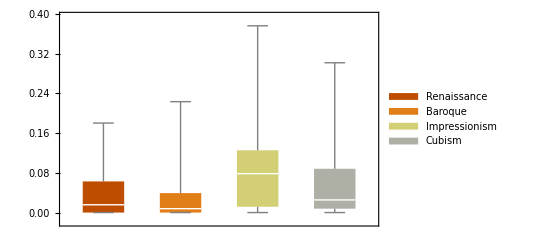

```mathematica
BoxWhiskerChart[{maxIntR,maxIntB,maxIntI,maxIntC},ChartStyle->40,ChartLegends->{"Renaissance","Baroque","Impressionism","Cubism"}]
```

As wee can see, the impressionism is the most compressed and lower high intensitie. The cubism is the period with higher intensities in its art. You can see the median of the boxplot is much higher that in other movements.

Show the boxplots of data of the maximum intensities of each period:

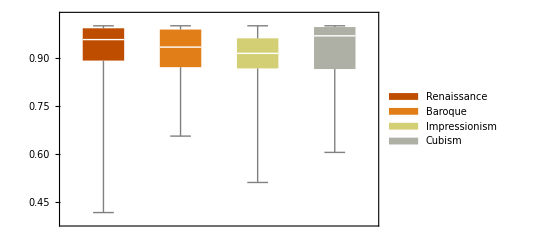

```mathematica
BoxWhiskerChart[{minIntR,minIntB,minIntI,minIntC},ChartStyle->40,ChartLegends->{"Renaissance","Baroque","Impressionism","Cubism"}]
```

the mean intesnsities of Renaissance and Baroque are lower than Impressionism and cubism.

Show the boxplots of data of the mean intensities of each period:

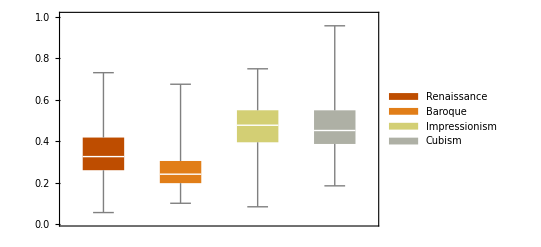

```mathematica
BoxWhiskerChart[{meanIntR,meanIntB,meanIntI,meanIntC},ChartStyle->40,ChartLegends->{"Renaissance","Baroque","Impressionism","Cubism"}]
```

In conclusion, Renaissance and Baroque are characterized by darkness of its colors, while the other two movements a less serious and transfer brighter feelings.

## Creating Classifier Functions for the Art Movements

To create a classifier function, we need two sets of data. One is used for training the function, we will call it the training data, and the second one is used for testing the function, which will be called the test data. With this last mentioned set we will be able to check the efficiency of the classifier function. We also need the sorted set of test data, which we save under the variable name testdataclassified, and which we will use below in future functions. We first do this analysis for a classifier of art movements, and then a classifier function for artists.

Create the associated list for training Classifier function:

```mathematica
trainingdata=<|"Impressionism"->impr⟦;;80⟧,"Renaissance"->renaissance⟦;;80⟧,"Barroque"->barroque⟦;;80⟧,"Cubism"->cubism⟦;;80⟧|>;
```

Create list for testing the function:

```mathematica
testdata=Join[RandomSample[impr⟦81;;⟧,12],RandomSample[renaissance⟦81;;⟧,12],RandomSample[barroque⟦81;;⟧,12],cubism⟦81;;⟧];
```

Create associated list of the test data to the region which it corresponds to:

```mathematica
testdataclassified=Join[Table[impr⟦i⟧->"Impressionism",{i,81,Length@impr}],Table[renaissance⟦i⟧->"Renaissance",{i,81,Length@renaissance}],Table[barroque⟦i⟧->"Barroque",{i,81,Length@barroque}],Table[cubism⟦i⟧->"Cubism",{i,81,Length@cubism}]];
```

Extract from set of test data equal sized sets corresponding to each art movement:

```mathematica
equaltestdatacl=Join[RandomSample[testdataclassified⟦;;115⟧,12],RandomSample[testdataclassified⟦116;;221⟧,12],RandomSample[testdataclassified⟦222;;378⟧,12],testdataclassified⟦378;;⟧];
```

Using the training data, we train the functions, by approach of distinct methods: the Automatic, which is a Logistic Regression, the one using support vector machine method, using a decision tree and the Bayes method

Create ClassifyFunction[] of art movements:

```mathematica
classifier=Classify[trainingdata]
```

ClassifierFunction[…]

```mathematica
classifierSV=Classify[trainingdata,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
classifierDT=Classify[trainingdata,Method->"DecisionTree"]
```

ClassifierFunction[…]

```mathematica
classifierBayes=Classify[trainingdata,Method->"NaiveBayes"]
```

ClassifierFunction[…]

To see the information of the classifiers I use the function ClassifierInformation[]. This function is not Listable, and to make the work slightly easier, I added the Listable attribute

Save what attributes does ClassifierInformation[] has:

```mathematica
Attributes[ClassifierInformation]
```

{Protected,ReadProtected}

Add the Listable attribute for ClassifierInformation[]

```mathematica
SetAttributes[ClassifierInformation,Listable]
```

Get information of the four ClassifyFunction[] we have created:

```mathematica
ClassifierInformation[{classifier,classifierBayes,classifierSV,classifierDT}]
```

{Classifier information
Input type | Image
Classes | ,,BarroqueCubismImpressionismRenaissance
Method | NearestNeighbors
Accuracy | 66.5 % ± 8.4 %
Loss | 0.797 ± 0.091
Single evaluation time | 783. ms/example
Batch evaluation speed | 2.55 examples/s
Classifier memory | 2.9 MB
Training examples used | 320 examples
Training time | 2 14
 | ,Classifier information
Input type | Image
Classes | ,,BarroqueCubismImpressionismRenaissance
Method | NaiveBayes
Accuracy | 68.1 % ± 8.3 %
Loss | 13.7 ± 5.4
Single evaluation time | 388. ms/example
Batch evaluation speed | 2.59 examples/s
Classifier memory | 3.7 MB
Training examples used | 320 examples
Training time | 1 56
 | ,Classifier information
Input type | Image
Classes | ,,BarroqueCubismImpressionismRenaissance
Method | SupportVectorMachine
Accuracy | 78.8 % ± 7.4 %
Loss | 0.591 ± 0.14
Single evaluation time | 371. ms/example
Batch evaluation speed | 2.81 examples/s
Classifier memory | 7.12 MB
Training examples used | 320 examples
Training time | 1 59
 | ,Classifier information
Input type | Image
Classes | ,,BarroqueCubismImpressionismRenaissance
Method | DecisionTree
Accuracy | 29.3 % ± 1.6 %
Loss | 1.51 ± 0.021
Single evaluation time | 351. ms/example
Batch evaluation speed | 2.86 examples/s
Classifier memory | 235. kB
Training examples used | 320 examples
Training time | 1 58
 | }

As we see, the method of NaiveBayes and Decision Tree we see that the learning curve decreases after the 60th iteration. The training of each network was between 2 and 3 minutes. Now I have to restore the attributes of the ClassifierInformation function

Restore attributes of ClassifierInformation:

```mathematica
Attributes[ClassifierInformation]={Protected,ReadProtected};
```

Check the efficiency of classifiers using the test data sets:

```mathematica
classifierm1=ClassifierMeasurements[classifier,equaltestdatacl]
classifierm2=ClassifierMeasurements[classifierBayes,equaltestdatacl]
classifierm3=ClassifierMeasurements[classifierMarkov,equaltestdatacl]
classifierm4=ClassifierMeasurements[classifierDT,equaltestdatacl]
```

ClassifierMeasurementsObject[…]

ClassifierMeasurementsObject[…]

ClassifierMeasurementsObject[…]

«1 more identical outputs»

Calculate the accuracy of classifiers:

```mathematica
{classifierm1["Accuracy"],classifierm2["Accuracy"],classifierm3["Accuracy"],classifierm4["Accuracy"]}
```

{0.518797,0.533835,0.609023,0.458647}

Show the Confusion Matrix Plot (the higher the numbers in the diagonal, the better the ClassifyFunction[] is):

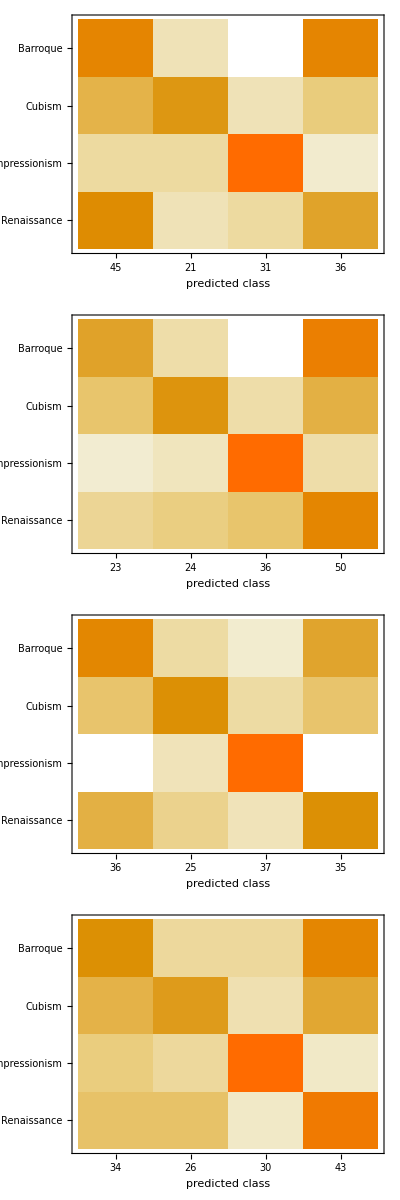

```mathematica
{classifierm1["ConfusionMatrixPlot"],classifierm2["ConfusionMatrixPlot"],classifierm3["ConfusionMatrixPlot"],classifierm4["ConfusionMatrixPlot"]}//TableForm
```

Note that the main mistakes made by the classifier functions was between the baroque and the renaissance periods. Indeed, these are art movements not very different from each other. Not every person would be able to classify for sure to which of the two periods it belongs. One has to have deeper knowledge, of the characteristics.

## Creating Classifier Functions for the Artists

```mathematica
paintors={vangogh,picasso,davinci,titian,rembrandt,rubens,caravaggio};
```

```mathematica
trainingdatapaintors=<|"Van Gogh"->vangogh⟦;;30⟧,"Picasso"->picasso⟦;;30⟧,"Titian"->titian⟦;;30⟧,"Rembrandt"->rembrandt⟦;;30⟧,"Rubens"->rubens⟦;;30⟧,"Caravaggio"->caravaggio⟦;;30⟧|>;
```

```mathematica
testdataclassifiedpaintors=Join[Table[vangogh⟦i⟧->"Van Gogh",{i,31,Length@vangogh}],Table[picasso⟦i⟧->"Picasso",{i,31,Length@picasso}],Table[barroque⟦i⟧->"Titian",{i,31,Length@titian}],Table[cubism⟦i⟧->"Rembrandt",{i,31,Length@rembrandt}],Table[cubism⟦i⟧->"Rubens",{i,31,Length@rubens}],Table[cubism⟦i⟧->"Caravaggio",{i,31,Length@caravaggio}]];
```

```mathematica
Length@vangogh-31
```

164

```mathematica
Length@testdataclassifiedpaintors
```

361

Extract from set of test data equal sized sets corresponding to each art movement:

```mathematica
equaltestdataPaintorscl=Join[RandomSample[testdataclassifiedpaintors⟦;;164⟧,12],RandomSample[testdataclassifiedpaintors⟦165;;205⟧,12],RandomSample[testdataclassifiedpaintors⟦206;;265⟧,12],testdataclassifiedpaintors⟦266;;284⟧,testdataclassifiedpaintors⟦285;;309⟧,testdataclassifiedpaintors⟦310;;361⟧];
```

```mathematica
classifierPaintors=Classify[trainingdatapaintors]
```

ClassifierFunction[…]

```mathematica
classifierPaintorsMarkov=Classify[trainingdatapaintors,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
classifierPaintorsDT=Classify[trainingdatapaintors,Method->"DecisionTree"]
```

ClassifierFunction[…]

```mathematica
classifierPaintorsBayes=Classify[trainingdatapaintors,Method->"NaiveBayes"]
```

ClassifierFunction[…]

Save what attributes does ClassifierInformation[] has:

```mathematica
Attributes[ClassifierInformation]
```

{Protected,ReadProtected}

Add the Listable attribute for ClassifierInformation[]

```mathematica
SetAttributes[ClassifierInformation,Listable]
```

Get information of the four ClassifyFunction[] we have created:

```mathematica
ClassifierInformation[{classifierPaintors,classifierPaintorsBayes,classifierPaintorsMarkov,classifierPaintorsDT}]
```

{Classifier information
Input type | Image
Number of classes | 6
Method | NearestNeighbors
Accuracy | 51.8 % ± 12. %
Loss | 1.37 ± 0.27
Single evaluation time | 369. ms/example
Batch evaluation speed | 3.14 examples/s
Classifier memory | 1.77 MB
Training examples used | 180 examples
Training time | 1 22
 | ,Classifier information
Input type | Image
Number of classes | 6
Method | NaiveBayes
Accuracy | 62.6 % ± 12. %
Loss | 39.4 ± 17.
Single evaluation time | 334. ms/example
Batch evaluation speed | 3. examples/s
Classifier memory | 3.27 MB
Training examples used | 180 examples
Training time | 1 1
 | ,Classifier information
Input type | Image
Number of classes | 6
Method | SupportVectorMachine
Accuracy | 70.7 % ± 11. %
Loss | 0.934 ± 0.22
Single evaluation time | 319. ms/example
Batch evaluation speed | 2.72 examples/s
Classifier memory | 7.54 MB
Training examples used | 180 examples
Training time | 1 17
 | ,Classifier information
Input type | Image
Number of classes | 6
Method | DecisionTree
Accuracy | 26.8 % ± 7.5 %
Loss | 1.91 ± 0.15
Single evaluation time | 324. ms/example
Batch evaluation speed | 3.17 examples/s
Classifier memory | 251. kB
Training examples used | 180 examples
Training time | 1 1
 | }

```mathematica
Attributes[ClassifierInformation]={Protected,ReadProtected}
```

{Protected,ReadProtected}

Check the efficiency of classifiers

```mathematica
classifierm11=ClassifierMeasurements[classifierPaintors,equaltestdataPaintorscl]
classifierm22=ClassifierMeasurements[classifierPaintorsBayes,equaltestdataPaintorscl]
classifierm33=ClassifierMeasurements[classifierPaintorsDT,equaltestdataPaintorscl]
classifierm44=ClassifierMeasurements[classifierPaintorsMarkov,equaltestdataPaintorscl]
```

ClassifierMeasurementsObject[…]

ClassifierMeasurementsObject[…]

ClassifierMeasurementsObject[…]

«1 more identical outputs»

Calculate the accuracy of classifiers:

```mathematica
{classifierm11["Accuracy"],classifierm22["Accuracy"],classifierm33["Accuracy"],classifierm44["Accuracy"]}
```

{0.265152,0.181818,0.166667,0.174242}

Show the Confusion Matrix Plot (the higher the numbers in the diagonal, the better the ClassifyFunction[] is):

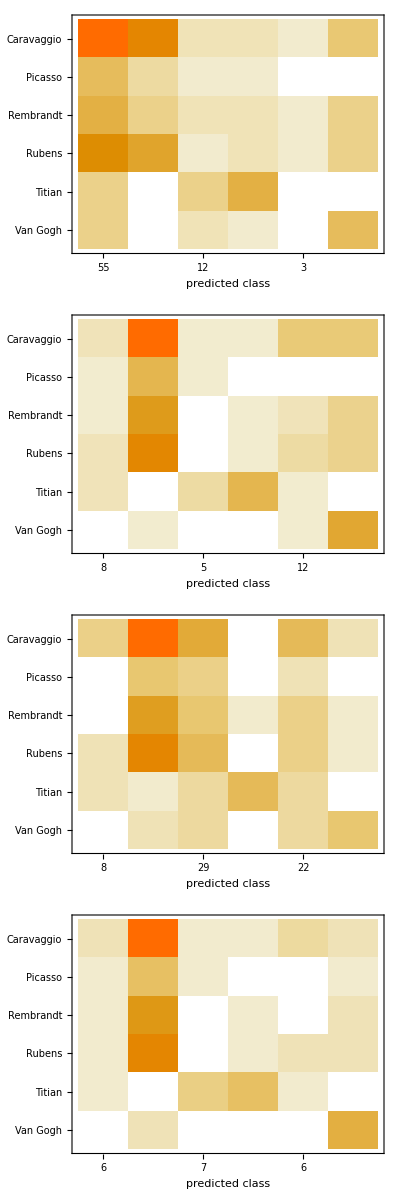

```mathematica
{classifierm11["ConfusionMatrixPlot"],classifierm22["ConfusionMatrixPlot"],classifierm33["ConfusionMatrixPlot"],classifierm44["ConfusionMatrixPlot"]}//TableForm
```

## Creating Classifier Functions

To create a classifier function, we need two sets of data. One used to train the function, we will call it the training data, and the second one would be the test data, with which we are able to check the efficiency of the classifier function. We also need the sorted set of test data, which we save under the variable name testdataclassified, and which we will use below in future functions. We first do this analysis for a classifier of art movements, and then a classifier function for artists.

```mathematica
trainingdata=<|"Impressionism"->impr⟦;;80⟧,"Renaissance"->renaissance⟦;;80⟧,"Barroque"->barroque⟦;;80⟧,"Cubism"->cubism⟦;;80⟧|>;
```

```mathematica
testdata=Join[RandomSample[impr⟦81;;⟧,12],RandomSample[renaissance⟦81;;⟧,12],RandomSample[barroque⟦81;;⟧,12],cubism⟦81;;⟧];
```

```mathematica
testdataclassified=Join[Table[impr⟦i⟧->"Impressionism",{i,81,Length@impr}],Table[renaissance⟦i⟧->"Renaissance",{i,81,Length@renaissance}],Table[barroque⟦i⟧->"Barroque",{i,81,Length@barroque}],Table[cubism⟦i⟧->"Cubism",{i,81,Length@cubism}]];
```

```mathematica
equaltestdatacl=Join[RandomSample[testdataclassified⟦;;115⟧,12],RandomSample[testdataclassified⟦116;;221⟧,12],RandomSample[testdataclassified⟦222;;378⟧,12],testdataclassified⟦378;;⟧];
```

```mathematica
Length@impr
Length@barroque
Length@cubism
Length@renaissance
```

Using the training data, we train the functions, by approach of distinct methods: the Automatic, which is a logistic Regression, the one using support vector machine method, using a decision tree and the Bayes method

```mathematica
classifier=Classify[trainingdata]
```

ClassifierFunction[…]

```mathematica
classifierMarkov=Classify[trainingdata,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
classifierDT=Classify[trainingdata,Method->"DecisionTree"]
```

ClassifierFunction[…]

```mathematica
classifierBayes=Classify[trainingdata,Method->"NaiveBayes"]
```

ClassifierFunction[…]

To see the information of the classifiers I use the function ClassifierInformation[]. This function is not Listable, and to make the work slightly easier, I added the Listable attribute

```mathematica
Attributes[ClassifierInformation]
```

{Protected,ReadProtected}

```mathematica
SetAttributes[ClassifierInformation,Listable]
```

```mathematica
ClassifierInformation[{classifier,classifierBayes,classifierMarkov,classifierDT}]
```

{Classifier information
Input type | Image
Classes | ,,BarroqueCubismImpressionismRenaissance
Method | NearestNeighbors
Accuracy | 66.5 % ± 8.4 %
Loss | 0.797 ± 0.091
Single evaluation time | 783. ms/example
Batch evaluation speed | 2.55 examples/s
Classifier memory | 2.9 MB
Training examples used | 320 examples
Training time | 2 14
 | ,Classifier information
Input type | Image
Classes | ,,BarroqueCubismImpressionismRenaissance
Method | NaiveBayes
Accuracy | 68.1 % ± 8.3 %
Loss | 13.7 ± 5.4
Single evaluation time | 388. ms/example
Batch evaluation speed | 2.59 examples/s
Classifier memory | 3.7 MB
Training examples used | 320 examples
Training time | 1 56
 | ,Classifier information
Input type | Image
Classes | ,,BarroqueCubismImpressionismRenaissance
Method | SupportVectorMachine
Accuracy | 78.8 % ± 7.4 %
Loss | 0.591 ± 0.14
Single evaluation time | 371. ms/example
Batch evaluation speed | 2.81 examples/s
Classifier memory | 7.12 MB
Training examples used | 320 examples
Training time | 1 59
 | ,Classifier information
Input type | Image
Classes | ,,BarroqueCubismImpressionismRenaissance
Method | DecisionTree
Accuracy | 29.3 % ± 1.6 %
Loss | 1.51 ± 0.021
Single evaluation time | 351. ms/example
Batch evaluation speed | 2.86 examples/s
Classifier memory | 235. kB
Training examples used | 320 examples
Training time | 1 58
 | }

As we see, the method of NaiveBayes and Decision Tree we see that the learning curve decreases after the 60th iteration. The training of each network was between 2 and 3 minutes. Now I have to restore the attributes of the ClassifierInformation function

```mathematica
Attributes[ClassifierInformation]={Protected,ReadProtected};
```

```mathematica
classifierm1=ClassifierMeasurements[classifier,equaltestdatacl]
classifierm2=ClassifierMeasurements[classifierBayes,equaltestdatacl]
classifierm3=ClassifierMeasurements[classifierMarkov,equaltestdatacl]
classifierm4=ClassifierMeasurements[classifierDT,equaltestdatacl]
```

ClassifierMeasurementsObject[…]

ClassifierMeasurementsObject[…]

ClassifierMeasurementsObject[…]

«1 more identical outputs»

```mathematica
{classifierm1["Accuracy"],classifierm2["Accuracy"],classifierm3["Accuracy"],classifierm4["Accuracy"]}
```

{0.518797,0.533835,0.609023,0.458647}

Here we can see the Confusion Matrix Plot.

```mathematica
{classifierm1["ConfusionMatrixPlot"],classifierm2["ConfusionMatrixPlot"],classifierm3["ConfusionMatrixPlot"],classifierm4["ConfusionMatrixPlot"]}//TableForm
```

-Graphics-

Note that the main mistakes made by the classifier functions was between barroque and renaissance, or cubism and impressionism, which indeed are art movements not far away from each other in time. But this task wouldn’t be able to classify even a normal person. One has to have deeper knowledge, of the characteristics. For instance, Barroque has ange

```mathematica
paintors={vangogh,picasso,davinci,titian,rembrandt,rubens,caravaggio};
```

```mathematica
Table[Length@paintors⟦i⟧,{i,1,7}]
```

{195,71,26,92,50,58,75}

```mathematica
trainingdatapaintors=<|"Van Gogh"->vangogh⟦;;30⟧,"Picasso"->picasso⟦;;30⟧,"Titian"->titian⟦;;30⟧,"Rembrandt"->rembrandt⟦;;30⟧,"Rubens"->rubens⟦;;30⟧,"Caravaggio"->caravaggio⟦;;30⟧|>;
```

```mathematica
testdataclassifiedpaintors=Join[Table[vangogh⟦i⟧->"Van Gogh",{i,31,Length@vangogh}],Table[picasso⟦i⟧->"Picasso",{i,31,Length@picasso}],Table[barroque⟦i⟧->"Titian",{i,31,Length@titian}],Table[cubism⟦i⟧->"Rembrandt",{i,31,Length@rembrandt}],Table[cubism⟦i⟧->"Rubens",{i,31,Length@rubens}],Table[cubism⟦i⟧->"Caravaggio",{i,31,Length@caravaggio}]];
```

```mathematica
classifierPaintors=Classify[trainingdatapaintors]
```

ClassifierFunction[…]

```mathematica
classifierPaintorsMarkov=Classify[trainingdatapaintors,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
classifierPaintorsDT=Classify[trainingdatapaintors,Method->"DecisionTree"]
```

ClassifierFunction[…]

```mathematica
classifierPaintorsBayes=Classify[trainingdatapaintors,Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[{classifierPaintors,classifierPaintorsBayes,classifierPaintorsMarkov,classifierPaintorsDT}]
```

{Classifier information
Input type | Image
Number of classes | 6
Method | RandomForest
Accuracy | 51.8 % ± 12. %
Loss | 1.63 ± 0.059
Single evaluation time | 371. ms/example
Batch evaluation speed | 2.74 examples/s
Classifier memory | 387. kB
Training examples used | 180 examples
Training time | 1 18
 | ,Classifier information
Input type | Image
Number of classes | 6
Method | NaiveBayes
Accuracy | 62.6 % ± 12. %
Loss | 39.4 ± 17.
Single evaluation time | 379. ms/example
Batch evaluation speed | 2.73 examples/s
Classifier memory | 3.27 MB
Training examples used | 180 examples
Training time | 1 6
 | ,Classifier information
Input type | Image
Number of classes | 6
Method | SupportVectorMachine
Accuracy | 62.6 % ± 12. %
Loss | 1.13 ± 0.13
Single evaluation time | 372. ms/example
Batch evaluation speed | 2.8 examples/s
Classifier memory | 7.81 MB
Training examples used | 180 examples
Training time | 1 15
 | ,Classifier information
Input type | Image
Number of classes | 6
Method | DecisionTree
Accuracy | 32.9 % ± 11. %
Loss | 1.82 ± 0.27
Single evaluation time | 348. ms/example
Batch evaluation speed | 2.89 examples/s
Classifier memory | 249. kB
Training examples used | 180 examples
Training time | 1 9
 | }

```mathematica
classifierm11=ClassifierMeasurements[classifier,equaltestdatacl]
classifierm22=ClassifierMeasurements[classifierBayes,equaltestdatacl]
classifierm33=ClassifierMeasurements[classifierMarkov,equaltestdatacl]
classifierm44=ClassifierMeasurements[classifierDT,equaltestdatacl]
```

ClassifierMeasurementsObject[…]

ClassifierMeasurementsObject[…]

ClassifierMeasurementsObject[…]

«1 more identical outputs»

## Combining two images with neural networks

And believe it or not, this is me traveling in time, I was painted by artists from the Renassaince to the Cubism period.

```mathematica
me=CurrentImage[]
```

-Graphics-

```mathematica
ImageRestyle[me,renaissance⟦20⟧]
```

-Graphics-

```mathematica
ImageRestyle[me,barroque⟦80⟧]
```

-Graphics-

```mathematica
ImageRestyle[me,cubism⟦50⟧]
```

-Graphics-

```mathematica
ImageRestyle[me,impr⟦50⟧]
```

-Graphics-

1	https://en.wikipedia.org/wiki/Renaissance

2	https://en.wikipedia.org/wiki/Baroque

3	https://en.wikipedia.org/wiki/Impressionism

4	https://en.wikipedia.org/wiki/Cubism

## Further explorations

Investigate other art movements.

Investigate the same but using other Methods in Classify[]

## Author contact information

Liubove Orlov Savko

liuba1156@gmail.com